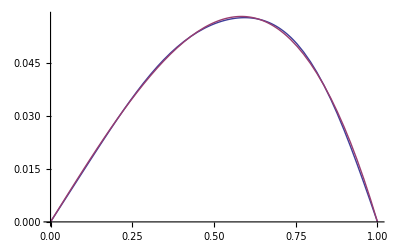

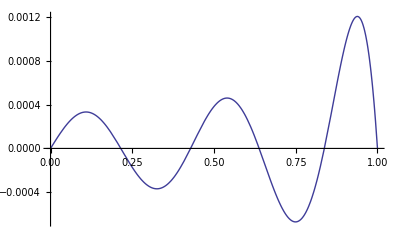

```mathematica
Phi=Table[Sin[i Pi x],{i,1,4}];
Plot[Phi,{x,0,1}];
Kij=Table[Integrate [D[Phi[[i]],x] D[ Phi[[j]],x]+Phi[[i]] Phi[[j]],{x,0,1}],{i,1,Length[Phi]},{j,1,Length[Phi]}];
Fj=Table[Integrate[x Phi[[j]],{x,0,1}],{j,1,Length[Phi]}];
alpha= LinearSolve[Kij,Fj];
vj= alpha.Phi;
Plot[{vj,x-(Sinh[x]/Sinh[1])},{x,0,1}]
Erro1=Plot[-vj+x-(Sinh[x]/Sinh[1]),{x,0,1}]
```

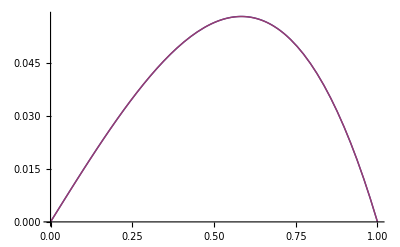

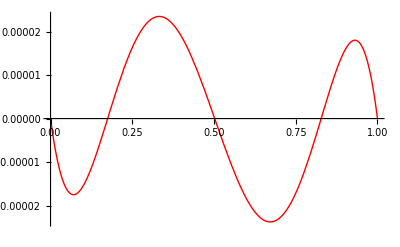

```mathematica
phi1=InterpolatingPolynomial[{{0,0},{0.5,1},{1,0}},x];
phi2=InterpolatingPolynomial[{{0,0},{0.25,0.5},{0.5,1},{1,0}},x];
phi3=InterpolatingPolynomial[{{0,0},{0.25,0.5},{0.5,0.8},{0.75,1},{1,0}},x];
Phi2={phi1,phi2,phi3};
Kij2=Table[Integrate [D[Phi2[[i]],x] D[ Phi2[[j]],x]+Phi2[[i]] Phi2[[j]],{x,0,1}],{i,1,Length[Phi2]},{j,1,Length[Phi2]}];
Fj2=Table[Integrate[x Phi2[[j]],{x,0,1}],{j,1,Length[Phi2]}];
alpha2= LinearSolve[Kij2,Fj2];
vj2= alpha2.Phi2;
Plot[{vj2,x-(Sinh[x]/Sinh[1])},{x,0,1}]
Erro2=Plot[-vj2+x-(Sinh[x]/Sinh[1]),{x,0,1},PlotStyle->RGBColor[1,0,0]]
```

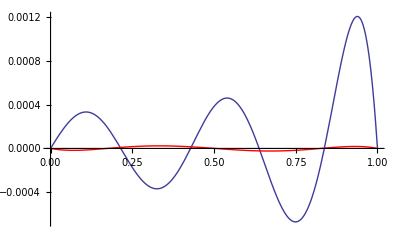

```mathematica
Show[Erro1,Erro2]
```